```mathematica
filename="E:\\Cavendish\\runs\\run3.MOV";
frames=Import[filename,"ImageList"];
```

```mathematica
Manipulate[ImageTake[frames[[1]],{a,b},{c,d}],{a,1,1080},{b,2,1080},{c,1,1920},{d,2,1920}]
```

```mathematica
length=Length[frames];
ymin=248;
ymax=290;
xmin=1;
xmax=1920;
croppedFrames=Table[ImageTake[frames[[i]],{ymin,ymax},{xmin,xmax}],{i,length}];
```

```mathematica
croppedFrames[[1]]
imgDim=ImageDimensions[croppedFrames[[1]]]
```

-Graphics-

{1920,43}

```mathematica
binarizedFrames=Table[Binarize[croppedFrames[[i]],.5],{i,length}];
newBinarizedFrames=Table[DeleteSmallComponents[binarizedFrames[[i]]],{i,length}];
```

```mathematica
help=Table[ComponentMeasurements[newBinarizedFrames[[i]],"Centroid"],{i,length}]//Values;
xvals=Flatten[help[[;;,;;,1]]];
yvals=Flatten[help[[;;,;;,2]]];
```

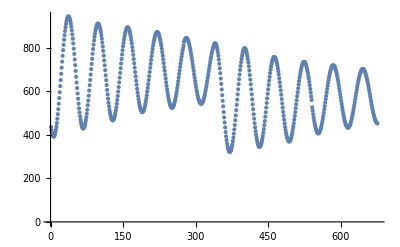

{435.5,421.,409.,400.167,394.833,392.,392.,395.167,401.167,410.833,422.25,437.167,453.833,473.5,494.5,517.5,542.5,568.7,595.3,623.5,651.5,680.,708.1,735.714,762.625,788.833,813.,836.333,857.1,876.167,893.667,908.9,920.9,930.,937.7,942.,943.214,942.,938.,931.1,922.125,910.,896.,879.333,861.,840.9,819.167,795.333,771.,745.7,719.667,693.,666.5,640.,614.3,589.5,565.7,542.833,521.7,502.5,484.833,469.5,456.833,445.3,437.833,432.,429.167,429.167,432.,436.167,443.5,453.5,466.1,480.5,497.167,515.,536.,557.,579.5,603.167,627.667,651.667,676.5,701.167,725.083,748.682,772.,793.667,814.,833.,849.833,865.,878.375,889.5,898.1,904.5,909.214,910.5,909.9,907.,901.833,893.667,884.,871.3,857.167,841.5,824.25,805.,785.1,763.5,741.5,719.167,696.333,673.,650.5,628.1,606.,585.333,565.7,547.,530.75,514.667,502.,490.,480.5,474.167,468.9,466.333,466.333,468.5,473.,479.5,488.,498.5,511.5,526.,542.167,560.,578.25,598.5,619.167,641.,662.,684.,705.643,727.25,748.136,768.5,787.75,806.1,822.5,838.071,851.5,863.375,873.3,881.5,887.3,891.,893.3,893.,890.,885.9,879.167,871.,860.1,848.333,834.167,819.5,802.7,785.5,766.9,747.5,727.833,708.1,688.,668.167,648.5,629.667,610.9,593.9,577.5,562.3,549.,537.3,526.5,518.3,512.,507.833,504.667,504.,505.3,509.,514.,521.25,530.667,541.167,553.5,567.1,581.75,598.25,615.,632.3,651.,669.333,688.667,707.5,725.654,743.5,761.333,778.333,794.,809.,822.1,833.833,844.,853.,860.3,865.833,869.5,871.3,871.167,869.5,865.833,860.,852.833,843.833,833.833,822.1,809.167,794.833,779.167,763.1,746.333,728.955,711.,693.833,675.833,658.1,641.,625.,608.9,594.5,580.333,567.9,556.833,547.,539.167,533.,528.167,525.167,524.,524.5,526.5,530.667,536.5,544.,552.5,562.9,574.3,587.3,600.333,615.375,630.5,646.5,662.833,679.167,695.333,711.833,727.955,743.318,758.071,772.667,785.75,797.5,809.,826.3,833.,838.214,841.5,843.643,843.833,843.,840.3,836.,829.75,822.1,813.333,803.1,792.1,780.,766.9,752.667,738.115,723.071,707.9,692.833,676.75,661.9,646.786,632.,618.667,604.9,593.9,582.167,572.333,563.3,556.75,551.,546.5,544.,542.,543.,544.,548.,552.1,558.5,566.1,575.25,584.214,596.,607.5,620.5,633.5,647.3,661.5,675.833,690.333,705.071,719.,732.429,746.,758.071,770.,780.786,790.333,799.,806.1,812.7,817.,820.,819.5,816.5,811.,802.25,791.643,778.5,763.167,745.625,726.167,705.071,683.,658.3,633.833,608.,581.7,556.,530.5,504.357,480.,456.5,433.833,412.3,392.833,376.,360.667,347.5,337.833,330.,324.167,321.,321.,323.3,328.5,335.,345.5,356.5,370.833,387.,405.167,424.5,444.833,466.7,489.,513.167,537.214,561.5,585.5,609.,632.5,655.,676.7,697.333,716.,733.667,748.5,762.5,774.,783.5,790.5,795.,797.167,796.5,794.667,789.5,781.5,772.167,760.7,746.643,731.1,714.,695.,674.5,653.357,631.5,608.75,585.5,562.5,539.5,517.,494.357,473.833,453.167,434.,416.833,400.5,386.7,374.5,364.3,355.7,350.,345.833,344.5,345.3,349.,353.7,360.9,370.3,381.7,395.,409.833,426.167,444.167,463.,483.,503.5,525.,546.,567.,588.3,608.9,629.,648.,665.7,683.167,698.5,712.3,723.962,734.75,743.056,749.5,755.,757.214,757.375,756.,752.1,747.,738.955,729.583,718.667,705.643,691.5,676.167,658.9,641.3,622.7,603.5,584.,563.7,544.,524.5,505.,486.5,469.167,452.,435.667,421.5,408.5,398.,388.167,381.,375.167,371.,369.,369.3,370.9,376.,382.,390.,399.7,410.7,423.833,437.833,452.5,469.5,486.167,504.,522.167,540.167,559.167,577.5,595.333,613.25,630.5,646.5,662.,676.,688.9,700.3,710.5,718.833,725.286,730.367,733.731,734.682,734.25,732.333,727.962,722.643,714.3,705.929,696.,684.7,671.5,657.9,642.75,627.,610.833,594.1,576.5,559.7,526.5,510.7,494.5,480.,466.5,454.167,443.167,433.167,425.,417.5,412.,408.3,406.7,406.5,407.3,410.5,416.,421.3,429.,439.,448.7,460.5,473.5,486.5,501.1,515.833,531.7,548.,563.3,578.5,594.9,610.75,625.333,639.833,652.5,665.214,676.5,686.667,695.5,703.1,710.,714.071,717.,719.167,719.167,716.5,714.,709.929,703.1,696.,687.071,677.5,666.833,654.5,642.,628.3,613.7,599.786,585.3,570.833,556.,541.5,527.3,513.625,501.,489.167,477.5,467.,458.167,451.,443.5,439.167,434.7,433.167,432.5,433.167,434.667,439.,443.,449.833,456.7,466.1,476.,486.167,497.7,510.5,523.167,536.333,550.,563.7,578.,591.3,604.7,618.,630.3,642.1,652.7,662.9,672.,680.333,687.071,692.833,697.3,700.3,702.167,702.167,701.25,699.167,695.1,690.333,684.25,676.5,668.5,659.,649.167,638.167,627.,614.3,602.1,589.214,576.333,563.5,551.3,538.5,526.5,514.5,504.667,494.3,486.,477.3,470.5,464.,459.167,456.,453.167,452.167}

E:\Cavendish\runs\run3data.csv

```mathematica
ListPlot[Transpose[xvals]]

dataset = Transpose[xvals]
Export["E:\\Cavendish\\runs\\run3data.csv",dataset,"CSV"]
```